# Progetto Matematica Computazionale a.a. 2025/2026

## Gioco interattivo - Riproduci l’immagine mostrata!

## Gruppo n°03 - Dynamic-V

## MC 2025/2026

Mattia Albertini, Giacomo Biribicchi, Orazio Andrea Capone, Erik Dervishi, Alex Rossi

(anno 1, curriculum A),  (anno 1, curriculum A),  (anno 2, curriculum A),  (anno 1, curriculum A), (anno 1, curriculum C)

## Indice

Indice

Obbiettivo del Gioco

Requisiti Tecnici

Set-up Notebook

Trasformazioni Immagini

Sfocatura (Blurring)

Rotazione

Applicazione Filtro Colore

Traslazione

Allenamento e Gioco interattivo

Allenamento

Gioco

Sitografia e Bibliografia

Approfondimenti

Commenti e lavoro futuro

Commenti

Lavoro futuro

## Obbiettivo del Gioco

Il progetto si propone di introdurre i fondamenti dell’elaborazione digitale delle immagini (computer grafica) a un pubblico generico, privo di pregresse conoscenze informatiche, attraverso un’esperienza ludica e accessibile. L’obiettivo del gioco consiste nell’allenare la capacità di riconoscere e riprodurre trasformazioni applicate a un’immagine — tra cui sfocatura, rotazione, traslazione e variazione cromatica — stimolando così la percezione visiva dell’utente in modo intuitivo e coinvolgente. L’interfaccia grafica, sviluppata interamente tramite le funzionalità dinamiche di Mathematica, accompagna l’utente attraverso le diverse fasi dell’applicazione — dalla selezione del database di immagini alla verifica della risposta, fino alla visualizzazione della classifica finale — senza richiedere alcuna interazione diretta con il codice sottostante.

## Requisiti Tecnici

Al fine del corretto funzionamento di questo notebook è necessario:

Avere una versione di Wolfram 14.3 o successive;

Avere una connessione internet (in quanto è possibile usufruire di immagini, direttamente scaricate da un web-database di Wolfram, per avere un bacino di immagini più ampio).

## Set-up Notebook

Prima di poter usufruire dell’apposita sezione ‘Allenamento e Gioco interattivo’, l’utente deve eseguire le operazioni nell’ordine presentato:

Inizializzazione dell’ambiente di notebook: l’utente deve cliccare sul bottone ‘Inizializza Ambiente’ per permettere il caricamento della directory di lavoro e dei pacchetti necessari per il corretto funzionamento del programma.

N.B. Prima di continuare attendere la comparsa del pop-up che indica la corretta inizializzazione dell’ambiente e cliccare sul pulsante ‘ok’.

Evaluation del notebook: l’utente deve quindi cliccare sul bottone ‘Valuta il Notebook’ per permettere la valutazione del notebook e quindi la corretta esecuzione delle funzionalità ‘Allenamento’ e ‘Gioco’.

```mathematica
Button[Style["▶  Inizializza Ambiente",FontSize->16,FontWeight->Bold,FontColor->White],Module[{dir},
(*1. Pulizia memoria*)
ClearAll["Global`*"];
(*2. Controllo e impostazione Directory di lavoro*)
dir=NotebookDirectory[];
If[dir==$Failed,
MessageDialog["Errore: directory del notebook non trovata!"];
Return[];
,
SetDirectory[dir];
(*Sicurezza extra:aggiungiamo la directory anche al $Path*)
If[Not[MemberQ[$Path,dir]],PrependTo[$Path,dir]];
];
(*3. Caricamento pacchetti*)
Get["TrasformazioneImmagini.wl"];
Get["Interfaccia.wl"];
(*4. Messaggio*)
MessageDialog[Style["✓  Ambiente inizializzato!",FontSize->14]];],Background->RGBColor[0.2,0.5,0.9],FrameMargins->15,ImageSize->{350,60},Method->"Queued"]
```

▶  Inizializza Ambiente

```mathematica
Button[Style["▶  Valuta il Notebook",FontSize->16,FontWeight->Bold,FontColor->White],FrontEndExecute[FrontEndToken[EvaluationNotebook[],"EvaluateNotebook"]],Background->RGBColor[0.2,0.5,0.9],FrameMargins->15,ImageSize->{250,60},Method->"Queued"]
```

▶  Valuta il Notebook

## Trasformazioni Immagini

## Sfocatura (Blurring)

La sfocatura, o blurring, è una tecnica di elaborazione delle immagini che consiste nel ridurre la nitidezza di un’immagine attenuando le variazioni brusche di intensità tra pixel adiacenti. Dal punto di vista matematico, l’operazione di blur corrisponde a una convoluzione dell’immagine originale con un apposito filtro, detto kernel. Il kernel più comunemente utilizzato è il filtro gaussiano, che assegna a ciascun pixel un nuovo valore calcolato come media pesata dei pixel vicini, con pesi distribuiti secondo una funzione gaussiana bidimensionale. Il risultato visivo è un’immagine progressivamente più “morbida” all’aumentare del parametro di sfocatura, poiché i dettagli ad alta frequenza — come bordi e texture — vengono progressivamente soppressi. In Mathematica questa operazione è implementata tramite la funzione Blur[image, r], dove r rappresenta il raggio di sfocatura, ovvero l’ampiezza del kernel gaussiano applicato.[1] [2] [3] [4]

```mathematica
Manipulate[modificaImmagine[Import["https://c8.alamy.com/compit/j253d8/esempio-illustrativo-del-timbro-j253d8.jpg"],raggioBlur,0,0,0,None,10],{{raggioBlur,0,"Intensità Blur"},0,40,1,Appearance->"Labeled"}, ContentSize->{150,150}]
SetOptions[NextCell[],Editable->False];
```

## Rotazione

La rotazione è una trasformazione geometrica che ruota tutti i pixel di un’immagine di un angolo θ attorno a un punto fisso, tipicamente il centro dell’immagine. A differenza della traslazione, che sposta l’immagine linearmente, la rotazione modifica la posizione di ciascun pixel mantenendo invariate le distanze dal centro di rotazione, preservando quindi forma e proporzioni dell’immagine originale.[5]

Un aspetto fondamentale nella rotazione digitale delle immagini è il problema dell’interpolazione: poiché le nuove posizioni dei pixel non cadono in generale su coordinate intere della griglia, è necessario stimare il valore di ciascun pixel a partire dai pixel vicini. Le tecniche di interpolazione più comuni sono la nearest-neighbor (che assegna il valore del pixel più vicino, veloce ma con perdita di qualità), la bilineare (che calcola una media pesata dei quattro pixel adiacenti) e la bicubica (che considera un intorno più ampio, producendo risultati più nitidi a costo di una maggiore complessità computazionale). Un ulteriore aspetto da gestire riguarda i bordi: i pixel che dopo la rotazione cadono al di fuori dell’area dell’immagine originale vengono tipicamente riempiti con un colore fisso (nero), producendo le caratteristiche aree scure agli angoli visibili nelle immagini ruotate. In Mathematica la rotazione è implementata tramite la funzione ImageRotate[image, θ], che gestisce automaticamente sia l’interpolazione che il riempimento dei bordi. [6] [7] [8]

```mathematica
Manipulate[modificaImmagine[Import["https://c8.alamy.com/compit/j253d8/esempio-illustrativo-del-timbro-j253d8.jpg"],0,rotazioneScelta,0,0,None,10],{{rotazioneScelta,0,"Rotazione"},0,330,30,Appearance->"Labeled"}, ContentSize->{150,150}]
SetOptions[NextCell[],Editable->False];
```

## Applicazione Filtro Colore

L’applicazione di un filtro colore è una tecnica di elaborazione delle immagini che consiste nel modificare la tonalità cromatica di un’immagine mantenendo invariata la struttura luminosa originale, ovvero le variazioni di luce e ombra che definiscono la forma e il volume dei soggetti rappresentati. Per ottenere questo effetto in modo controllato e intuitivo, è conveniente operare non nello spazio colore RGB (Red, Green, Blue), nel quale i tre canali sono strettamente intrecciati, bensì nello spazio HSV (Hue, Saturation, Value), che separa esplicitamente la componente cromatica (Hue), la saturazione (Saturation) e la luminosità (Value). [9] [10] [11]

In questo spazio, applicare un filtro colore significa sostituire il valore di Hue — che rappresenta la tonalità pura, codificata come angolo su una ruota dei colori — con quello del colore desiderato, mantenendo invece invariato il valore di Value, che porta l’informazione di luminosità originale del pixel. In questo modo i pixel chiari dell’immagine originale risulteranno chiari nella versione colorata, e quelli scuri rimarranno scuri, preservando la leggibilità visiva dell’immagine. La Saturation controlla invece l’intensità del colore applicato: valori alti producono tinte vivide, valori bassi tendono al grigio. In Mathematica questa operazione è implementata tramite la funzione Colorize[image, ColorFunction -> ...], che permette di applicare una funzione colore pixel per pixel, combinata con ColorConvert per la conversione tra spazi colore. [12] [13] [14]

```mathematica
Manipulate[modificaImmagine[Import["https://c8.alamy.com/compit/j253d8/esempio-illustrativo-del-timbro-j253d8.jpg"],0,0,0,0,coloreScelto,10],{{coloreScelto,None,"Colore Immagine"},{None,Red,Green,Blue,Yellow,Cyan,Magenta,Orange}}, ContentSize->{150,150}]
SetOptions[NextCell[],Editable->False];
```

## Traslazione

La traslazione è una trasformazione geometrica che consiste nello spostamento di tutti i pixel di un’immagine di una quantità fissa lungo gli assi orizzontale e verticale. Formalmente, dato un pixel di coordinate (x,y), la traslazione di vettore (tx,ty) lo mappa nelle nuove coordinate (x+tx, y+ty)​. A differenza di altre trasformazioni geometriche come la rotazione o il ridimensionamento, la traslazione è una trasformazione affine nella sua forma più semplice, che preserva distanze, angoli e parallelismo tra le linee. [15] [16]

Un aspetto critico nella traslazione digitale delle immagini riguarda la gestione dei bordi: i pixel che vengono spostati oltre i limiti dell’immagine devono essere trattati in qualche modo. Le strategie più comuni includono il riempimento con un colore fisso (tipicamente nero), la riflessione ai bordi, oppure il cosiddetto wrap-around (o tiling), che consiste nel fare “rientrare” dall’altro lato i pixel che escono dal bordo opposto, trattando l’immagine come se fosse disposta su una superficie toroidale. Nel progetto è stata adottata proprio quest’ultima strategia, implementata tramite la funzione RotateRight di Mathematica applicata alla matrice dei pixel, che permette di ottenere la traslazione ciclica in modo efficiente senza richiedere operazioni di copia o padding esplicito. [17] [18]

```mathematica
Manipulate[modificaImmagine[Import["https://c8.alamy.com/compit/j253d8/esempio-illustrativo-del-timbro-j253d8.jpg"],0,0,xScelta,yScelta,None,11],{{xScelta,0,"Trasla X"},0,10,1,Appearance->"Labeled"}, {{yScelta,0,"Trasla Y"},0,10,1,Appearance->"Labeled"}, ContentSize->{150,150}]
SetOptions[NextCell[],Editable->False];
```

## Allenamento e Gioco interattivo

## Allenamento

### Tutorial Allenamento

In questa sezione è possibile provare applicare le varie trasformazioni, per capire bene come ogniuna di esse funziona e come esse interagiscono tra di loro. Si può optare per lavorare sull’immagine di test standard oppure caricarne una propria tramite il pulsante ‘Carica Immagine’.

L’utente può anche usufruire del tasto ‘Pulisci’ per portare l’immagine che sta modificando alle condizioni originali.

### Allenamento interattivo

```mathematica
Studia[]
SetOptions[NextCell[],Editable->False];
```

## Gioco

### Tutorial Gioco

Di seguito l’utente può verificare le proprie capacità mediante il gioco presentato: viene fornita un’immagine, a cui sono applicate delle trasformazioni in modo casuale, e l’obiettivo dell’utente è quello, fornita la stessa immagine ma senza che vi siano applicate le trasformazioni, di riprodurre la prima mediante le funzionalità disponibili.

Ogni partita ha un numero illimitato di livelli, permettendo di competere per il punteggio più alto, ogni livello ha immagini e trasformazioni diverse.

Prima di poter accede alla schermata di gioco, è però necessario:

Impostare il database presso cui le immagini vengono selezionate. L’utente con l’apposito menù a tendina, vicino alla scritta ‘Sorgente immagini’, può selezionare un database Web (attraverso cui le immagini vengono fornite direttamente dal database di Wolfram) oppure un database locale (attraverso cui le immagini vengono caricate direttamente dalla cartella ‘img’ nella stessa directory di questo notebook) e cliccare su ‘Carica database’ per avviare il caricamento.

N.B. per il database Web è necessaria una connessione internet ed aspettare qualche minuto che si avvenuto il corretto download delle corrispondenti immagini.

Impostare il valore ‘seed’. Il seed è un valore iniziale utilizzato da un algoritmo per generare una sequenza di numeri casuali. Se si usa lo stesso seed, si otterrà sempre gli stessi numeri. Questo permette al sistema di decidere da quale immagine far partire il gioco e come attuare le trasformazioni sull’immagine da riprodurre.

Impostare il ‘Nome giocatore’ ai fini della tracciabilità della classifica generale.

Dopo avere effettuato i precedenti passaggi, l’utente può quindi avviare la partita cliccando sul tasto ‘Nuova partita’.

N.B. con ‘partita’ si intende una sessione di gioco, ovvero una serie di round sucessivi che forniscono un punteggio che terminano solo quando l’utente usa l’apposito tasto ‘Termina Partita’.

La schermata che appare, oltre a presentare le stesse funzionalità di quelle presenti nella sezione ‘Allenamento’, propone anche delle nuove funzionalità:

Il pulsante ‘Mostra soluzione’ permette di vedere quali sono i valori delle trasformazioni applicate sull’immagine da riprodurre, una volta premuto non permetterà di guadagnare punti dall’esercizio;

Il pulsante ‘Risolvi esercizio’ permette di impostare ogni slider al valore corretto per la soluzione, analogamente a ‘Mostra soluzione’ una volta premuto non permetterà di guadagnare punti dall’esercizio;

Il pulsante ‘verifica’ permette di verificare se le trasformazioni applicate dall’utente corrispondano a quelle applicate sull’immagine da riprodurre. Se la verifica restituisce un risultato positivo vengono assegnati da 0 a 5 punti (in base a quanti ‘aiuti’ si sono usufruiti) e si passa ad un round successivo, altrimenti appare un pop-up che segnala l’errore.

Il pulsante ‘next’ permette di passare ad un round successivo senza effettuare la corretta verifica dell’immagine come citato precedentemente;

I pulsanti ‘aiuto’ forniscono un suggerimento all’utente impostando il valore corretto della relativa trasformazione.

N.B. ogni utilizzo di questo pulsante toglie un punto dal punteggio finale (fino ad un massimo di 5);

Il pulsante ‘pulisci Immagine’ serve per riportare l’immagine, del turno attuale, ai parametri iniziali dei valori delle trasformazioni.

Infine, premendo il pulsante ‘Termina Partita’, l’utente può terminare la propria sessione di gioco. 

Al termine della sessione di gioco appare a schermo la classifica che tiene traccia dei dieci migliori giocatori e dei loro punteggi.

N.B se si vuole iniziare una nuova partita bisogna prima terminare quella corrente attraverso il tasto apposito.

### Gioco Interattivo

```mathematica
Gioca[]
SetOptions[NextCell[],Editable->False];
```

## Sitografia e Bibliografia

## Sfocatura (Blurring)

↑  [1] Gonzalez, R. C., Woods, R. E. — Digital Image Processing, 4.aa ed., Pearson, 2018 https://www.cl72.org/090imagePLib/books/Gonzales,Woods-Digital.Image.Processing.4th.Edition.pdf

↑  [2]  Wolfram Documentation — Blur: https://reference.wolfram.com/language/ref/Blur.html

↑  [3]  Wolfram Documentation — GaussianFilter: https://reference.wolfram.com/language/ref/GaussianFilter.html

↑  [4]  Shapiro, L., Stockman, G. — Computer Vision, Prentice Hall, 2001 https://dl.acm.org/doi/book/10.5555/558008

## Rotazione

↑  [5]  Gonzalez, R. C., Woods, R. E. — Digital Image Processing, 4.aa ed., Pearson, 2018 https://www.cl72.org/090imagePLib/books/Gonzales,Woods-Digital.Image.Processing.4th.Edition.pdf

↑  [6]  Szeliski, R. — Computer Vision: Algorithms and Applications, 2.aa ed., Springer, 2022. Disponibile online: https://szeliski.org/Book/

↑  [7]  Burger, W., Burge, M. J. — Digital Image Processing: An Algorithmic Introduction, 3.aa ed., Springer, 2022 https://www.researchgate.net/publication/362216328_Digital_Image_Processing_An_Algorithmic_Introduction

↑  [8]  Wolfram Documentation — ImageRotate: https://reference.wolfram.com/language/ref/ImageRotate.html

## Applicazione filtro colore

↑  [9]  Gonzalez, R. C., Woods, R. E. — Digital Image Processing, 4.aa ed., Pearson, 2018 https://www.cl72.org/090imagePLib/books/Gonzales,Woods-Digital.Image.Processing.4th.Edition.pdf

↑  [10]  Szeliski, R. — Computer Vision: Algorithms and Applications, 2.aa ed., Springer, 2022. Disponibile online: https://szeliski.org/Book/

↑  [11]  Smith, A. R. — Color Gamut Transform Pairs, SIGGRAPH, 1978 — articolo fondativo dello spazio colore HSV https://www.researchgate.net/publication/233784968_Color_Gamut_Transform_Pairs

↑  [12]  Wolfram Documentation — Colorize: https://reference.wolfram.com/language/ref/Colorize.html

↑  [13]  Wolfram Documentation — ColorConvert: https://reference.wolfram.com/language/ref/ColorConvert.html

↑  [14]  Wolfram Documentation — Hue: https://reference.wolfram.com/language/ref/Hue.html

## Traslazione

↑  [15]  Gonzalez, R. C., Woods, R. E. — Digital Image Processing, 4.aa ed., Pearson, 2018 https://www.cl72.org/090imagePLib/books/Gonzales,Woods-Digital.Image.Processing.4th.Edition.pdf

↑  [16]  Szeliski, R. — Computer Vision: Algorithms and Applications, 2.aa ed., Springer, 2022. Disponibile online: https://szeliski.org/Book/

↑  [17]  Wolfram Documentation — RotateRight: https://reference.wolfram.com/language/ref/RotateRight.html

↑  [18]  Wolfram Documentation — ImageTransformation: https://reference.wolfram.com/language/ref/ImageTransformation.html

## Approfondimenti

HoldFirst e HoldAll
Gli attributi HoldFirst e HoldAll permettono di disabilitare la valutazione anticipata degli argomenti di una funzione. Per default, Mathematica valuta tutti gli argomenti prima di passarli alla funzione chiamata; questi attributi consentono invece di passare il simbolo così com’è, senza valutarlo. Il comportamento è concettualmente analogo al passaggio per riferimento presente in altri linguaggi di programmazione.

SystemDialogInput
SystemDialogInput apre la finestra di dialogo nativa del sistema operativo per la selezione di file, garantendo un’esperienza utente coerente con le convenzioni del sistema in uso. È stata inoltre specificata l’opzione Method -> “Queued”, che delega il caricamento a una coda separata rispetto al thread principale, prevenendo problemi di timeout durante l’importazione di file di grandi dimensioni.

Entity, EntityValue ed EntityList
Il sistema Entity di Mathematica fornisce un’interfaccia uniforme per accedere alla vasta base di dati strutturati del Wolfram Knowledgebase, una collezione di dati curati e aggiornati che spazia da specie animali a elementi chimici, da paesi a film. Ogni entità è identificata da un oggetto Entity[tipo, nome], dal quale è possibile estrarre proprietà specifiche — come immagini, descrizioni o dati numerici — tramite la funzione EntityValue. Le entità possono essere raggruppate in classi tramite EntityClass, che permette di filtrare sottoinsiemi omogenei all’interno di un dominio, e recuperate come lista tramite EntityList.

## Commenti e lavori futuri

## Commenti

HoldFirst e HoldAll
Nel progetto questo meccanismo si è rivelato essenziale per permettere ai controlli grafici dell’interfaccia di aggiornare direttamente le variabili di stato del DynamicModule. https://reference.wolfram.com/language/ref/HoldFirst.html

SystemDialogInput
Nel progetto questo meccanismo è risultato necessario al fine di offrire un’interazione intuitiva tra interfaccia ed utente. https://reference.wolfram.com/language/ref/SystemDialogInput.html?q=SystemDialogInput

Accessibilità
Nella progettazione dell’interfaccia si è prestata attenzione agli aspetti di accessibilità visiva. È stato adottato un font Sans Serif per migliorare la leggibilità per gli utenti affetti da dislessia. La codifica cromatica dei bottoni segue le convenzioni visive comunemente associate a determinate funzionalità — rosso per azioni terminali, verde per conferme. L’allineamento dei testi è stato impostato a sinistra per evitare spaziature irregolari che potrebbero ostacolare la lettura.

Gestione della memoria
Per evitare rallentamenti dovuti all’accumulo in memoria di copie ridondanti delle immagini modificate, è stata adottata una strategia di sovrascrittura delle variabili: anziché allocare nuove aree di memoria ad ogni aggiornamento, il contenuto della variabile viene sovrascritto con il nuovo valore. A questo si affianca il meccanismo interno di garbage collection di Mathematica, che libera automaticamente la memoria occupata da oggetti non più referenziati, mantenendo l’occupazione di memoria sotto controllo anche in sessioni prolungate.

Entity   
Nel progetto il sistema Entity è stato scelto come sorgente per il database di immagini web, in quanto garantisce immagini di qualità omogenea associate a soggetti ben definiti e riconoscibili. Un aspetto critico emerso durante lo sviluppo riguarda la dimensione dei batch: domini generici come “Species” o “Person” contengono centinaia di migliaia di entità, rendendo il caricamento dell’intera lista proibitivo. Per ovviare a questo problema si è ricorso a due strategie complementari: l’utilizzo di sottoclassi specifiche tramite EntityClass — come “MammalSpecies” per le specie o “Element” per gli elementi chimici — che circoscrivono il dominio a insiemi di dimensione ragionevole, e l’utilizzo di SampledEntityClass, che estrae un campione casuale di dimensione fissa senza scaricare l’intera lista. Inoltre, poiché non tutte le entità dispongono di un’immagine associata nel Knowledgebase, è stata implementata la funzione filterWithImages, che filtra preventivamente le entità prive di immagine tramite EntityValue e ImageQ, garantendo che il database finale contenga esclusivamente entità con immagine effettivamente disponibile. https://reference.wolfram.com/language/ref/Entity.html

Scelta del formato .wl per i package (invece che .m) 
I package Mathematica possono essere salvati con estensione .m o .wl. Il formato .m è il formato storico, ma essendo condiviso con MATLAB può generare ambiguità nei tool di sviluppo e nei sistemi di controllo versione. Il formato .wl (Wolfram Language) è invece il formato ufficialmente raccomandato da Wolfram a partire dalla versione 10, e identifica inequivocabilmente il file come codice Wolfram Language. Per queste ragioni, nel progetto si è scelto di adottare .wl, privilegiando chiarezza semantica e coerenza con le convenzioni della documentazione ufficiale. https://reference.wolfram.com/language/ref/format/WL.html

Diagramma delle dipendenze dei pacchetti:
Per garantire una struttura chiara e ordinata, abbiamo adottato il design pattern MVC (Model-View-Controller), suddividendo il progetto in tre componenti distinte:
	View: Gestita dal package Interfaccia, che si occupa esclusivamente della componente visiva e grafica del software.
	Model: Delegata ai package Classifica e Trasformazione Immagini, che racchiudono tutta la logica applicativa e l’elaborazione dei dati.
	Controller: Implementato all’interno del notebook, che funge da intermediario gestendo l’interazione diretta con l’utente.
Per permettere questa comunicazione fluida, le funzioni chiave dei package sono state definite come pubbliche. Questa scelta architetturale non solo rende il codice altamente modulare, ma offre un importante vantaggio in termini di riuso: i moduli di classificazione e trasformazione delle immagini sono completamente indipendenti e pronti per essere utilizzati da qualsiasi altro utente nell’ambiente Mathematica.

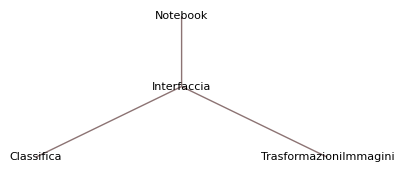

```mathematica
TreeForm[Notebook[Interfaccia[Classifica,TrasformazioniImmagini]]]
```

## Lavori futuri

Il progetto presentato può essere facilmente migliorato, ad esempio attraverso:

L’aggiunta di altre trasformazioni, oltre a quelle già presentate, come il ‘negativo dell’immagine’ o la ‘saturazione’.

L’aggiunta di ‘livelli di difficoltà’ andando ad esempio a ridurre o incrementare il numero di scelte possibili per i parametri delle trasformazioni da applicare, oppure riducendo il numero di aiuti possibili.

L’aggiunta di una classifica web che si aggiorna, e si sincronizza, in base alle sessioni di gioco effettuate su dispositivi differenti.